```mathematica
ℏ=6.63 10^-34/2/Pi;
kb=1.38 10^-23;
e=1.6 10^-19;
m=9.1 10^-31;
aem=1.66 10^-27;
Na=6.02 10^23;
```

```mathematica
w0=10^-3;
λ=532 10^-9;
R0=10^10;
zR=Pi w0^2/λ;
aR=10^-2;
k=2Pi/λ;
Cn=1.28 10^□;
H = 400 10^3;
h = 156;
r0 = 5 10^-2;
VWind=27;
```

```mathematica
wzsq[z_]:=w0^2((1-z/R0)^2+(z/zR)^2)
```

```mathematica
ηdif[z_]:=1.-Exp[-2 aR^2/wzsq[z]]
```

```mathematica
ηdif[400 10^3]
```

4.359×10^-8

```mathematica
σrysq[z_]:=1.23 Cn^2 k^(7/6)z^(11/6)
```

```mathematica
Cn2[h_]:=0.00594 ((VWind/27)^2(10^-5 h)^10 Exp[-h/1000]+2.7 10^-16 Exp[-h/1500]+A Exp[-h/100]m)
```

```mathematica
0.2/3.3 4096
```

248.242

```mathematica
100/16.
```

6.25

```mathematica
700/600.
```

1.16667

```mathematica
2/1.16
```

1.72414

```mathematica
600/4096. 3.3
```

0.483398

```mathematica
0.54(H-h)^2 Sec[0]^2(λ/w0)^2(w0/r0)^(5/3)
```

36.0066

```mathematica
ClearAll[p]
```

```mathematica
comp[ml_,wl_,bre_]:=Module[
{
probs={0,0.5,1},
qual,truth
}
,
(*качество алгоритма*)
qual[x_,p_]:=wl/((wl+x)-(bre-(wl+x) p));


Plot[qual[x,#]&/@probs//Evaluate,{x,0,4},PlotLegends->probs];

(*вероятность, что я могу верить полученному биту*)
truth[x_,p_]:=((wl+x)(1-p)+bre)/(wl+x);
Plot[truth[x,#]&/@probs//Evaluate,{x,0,4},PlotLegends->probs];

Plot[{qual[ml-wl,p],truth[ml-wl,p],qual[ml-wl,p]truth[ml-wl,p]wl/ml},{p,0,1},PlotLegends->{"qual","truth","qual×truth×rate"}]
]
```

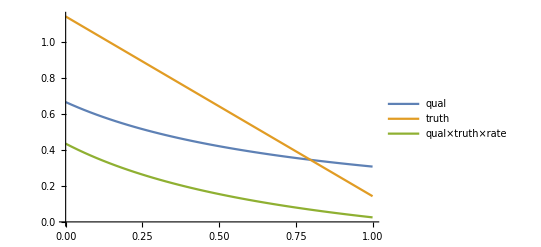

```mathematica
comp[7,4,1]
```

```mathematica
comp[21,12,3]
```

-Graphics-

```mathematica
ClearAll[wl,ml,bre]
```